# dual method for 2D penrose (5-fold)

Let’s first define basis vectors

```mathematica
a=2Pi/5;
r1={1,0};
r2={Cos[a],Sin[a]};
r3={Cos[2a],Sin[2a]};
r4={Cos[3a],Sin[3a]};
r5={Cos[4a],Sin[4a]};
vertices={r1,r2,r3,r4,r5};
basis =Graphics[Arrow[{{0,0},#}]&/@vertices,Axes->True];
```

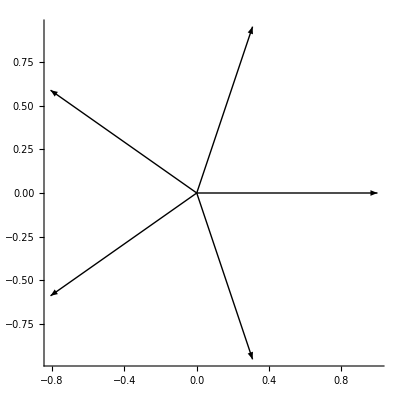

```mathematica
Show[basis, AspectRatio->1]
```